```mathematica
ClearAll["Global`*"]
```

## Evaluating the Rate of Stress vs Transition temperature

```mathematica
(*The objective here is to get the stress strian behaviour. First we do the Stress vs Transition temp behaviour*)
-Graphics-
```

```mathematica
(*Trail 1*)
```

```mathematica
σ:={0.03125,0.2265625,0.3203125,0.3828125,0.421875,0.453125,0.4765325,0.5}(*In GPa*)
```

```mathematica
Subscript[θ, c]:={1.5,1.6,1.75,1.875,2,2.125,2.25,2.375}(*In K*)
```

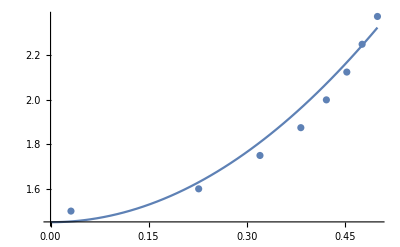

```mathematica
plt11=ListPlot[Transpose@{σ,Subscript[θ, c]}];(*Transition temp vs strain*)
plt12=Plot[{1.45+3.5*(x-0.0)^2,0.007},{x,0,σ[[Length[σ]]]}];
Show[plt11,plt12]
```

```mathematica
(*Trail 2*)
```

```mathematica
(*σ1:={0.0859375,0.2421875,0.328125,0.38671875,0.421875,0.453125,0.484375,0.50625,0.529296875,0.55,0.5703125,0.58984375}(*In GPa*)*)
```

```mathematica
σ1:={0.0625+0.03125-0.0078125,0.25-0.0078125*5/4,0.25+0.0625+0.015625+1/4*0.0078125,0.25+0.125+5/3*0.0078125,0.25+0.125+0.0625-0.015625,0.25+0.125+0.0625+0.015625,0.5-0.015625-1/3*0.0078125,0.5+1/3*0.0078125,0.5+0.0015625+3/2*0.0078125,0.5+0.0625-3/2*0.0078125,0.5+0.0625+0.0078125,0.5+0.0625+0.03125-2/3*0.0078125}(*In GPa*)
```

```mathematica
Subscript[θ1, c]:={1.5,1.625,1.75,1.875,2,2.125,2.25,2.375,2.5,2.625, 2.75,2.875}(*In K*)
```

```mathematica
Ds1=Range[Length[σ1]-1];
```

```mathematica
Ds1[[2]]
```

2

```mathematica
For[i=1,i<=Length[σ1]-1,i++,Ds1[[i]]=σ1[[i+1]]-σ1[[i]]]
```

```mathematica
Ds1
```

{0.154297,0.0898438,0.0579427,0.0338542,0.03125,0.0286458,0.0208333,0.0106771,0.0375,0.0195313,0.0182292}

```mathematica
(*Ds1[[1]]=0.1484375*)
```

```mathematica
Length[Ds1]
```

11

```mathematica
dtbds=Range[Length[σ1]-1]; (*dθ/dσ*)
```

```mathematica
θstar=Range[Length[σ1]-1];(*θ^* corresponding to the y coordinate of the point which has the same slope as the discrete slope calculated above.*)
```

```mathematica
For[i=1,i<=Length[σ1]-1,i++,dtbds[[i]]=(Subscript[θ1, c][[i+1]]-Subscript[θ1, c][[i]])/(σ1[[i+1]]-σ1[[i]]);θstar[[i]]=(Subscript[θ1, c][[i+1]]+Subscript[θ1, c][[i]])/2]
```

```mathematica
dtbds
```

{0.810127,1.3913,2.1573,3.69231,4.,4.36364,6.,11.7073,3.33333,6.4,6.85714}

```mathematica
dtbds[[1]]=0.125+0.03125-6/5*0.0078125 (*While the other Rolle Points are at the midpoint, the first one isnt quite at the midpoint.*)
```

0.146875

```mathematica
θstar[[1]]=2-11/3*0.0078125
```

1.97135

```mathematica
θstar
```

{1.97135,1.6875,1.8125,1.9375,2.0625,2.1875,2.3125,2.4375,2.5625,2.6875,2.8125}

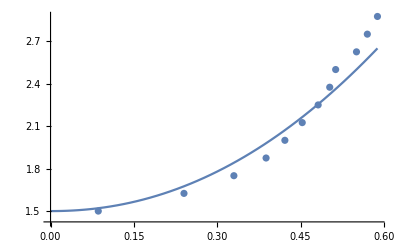

```mathematica
plt21=ListPlot[Transpose@{σ1,Subscript[θ1, c]},AxesLabel->Automatic];(*Transition temp vs strain*)
plt22=Plot[{1.5+3.5*(x-0.0)^2.1},{x,0,σ1[[Length[σ1]]]}];
Show[plt21,plt22]
```

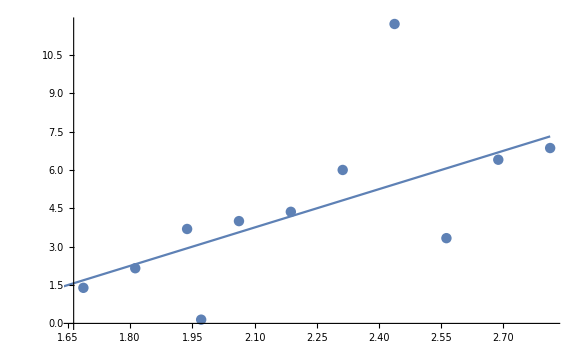

```mathematica
plt31=ListPlot[Transpose@{θstar,dtbds}];(*Transition temp Subscript[θ, c] vs Subscript[dθ, c]/dσ*)
plt32=Plot[{1/0.2*(x-1.35)},{x,0,θstar[[Length[θstar]]]}];
Show[plt31,plt32]
```

```mathematica
(*Note that since the first and the last few do not fall on this line, we will only match for the intermediate region.*)
```